-k+k^3.1

{{k→-0.988831-0.149042 ⅈ},{k→-0.988831+0.149042 ⅈ},{k→1.},{k→0.}}

1.25

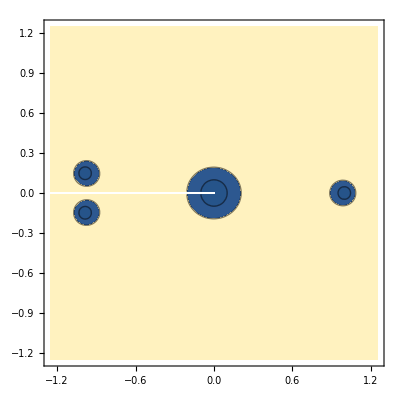

-k+k^3.14

{{k→-0.978954-0.204081 ⅈ},{k→-0.978954+0.204081 ⅈ},{k→1.},{k→0.}}

1.25

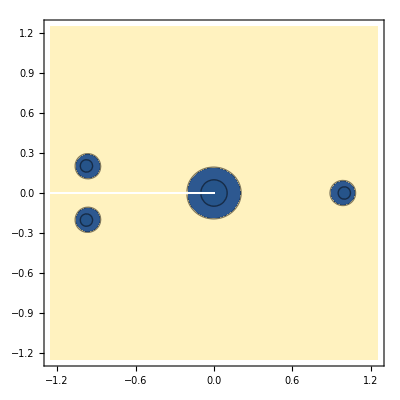

-k+k^3.14159

```mathematica
Clear[f]
f[k_] = k^3.1-k
NSolve[f[k]==0,k]
d = 1.25
ComplexContourPlot[Abs[f[k]],{k,-d-d I,d+d I},Contours->{0.1,0.2}]

f[k_] = k^2.1-1
NSolve[f[k]==0,k]
d = 1.25
ComplexContourPlot[Abs[f[k]],{k,-d-d I,d+d I},Contours->{0.1,0.2}]
```